```mathematica
Solve[(x/(G*M))/(1+(1+(2*x*e)/(G*M)^2)^0.5)==R,x]
```

{{x→2. R (1. G M+1. e R)}}

```mathematica
Integrate[(1-x/(2*e*r^2))^0.5,{x,0,2*e*r^2}]
```

1.33333 e r^2

```mathematica
(*COMPARISON FOR VARIOUS STELLAR OBJECTS*)

(*For Sun*)


R=6.95*10^8(*radius  in m*);
M=2*10^30 (*mass  in kg*);
vbar=3*10^5 (*mean velocity of halo in m/s*);
G=6.67*10^-11 (*Gravivational Constant in SI*);
μ=10 (*For WIMP mass 10 Gev*);

ee=(G*M)/R;
μ1=(μ+1)/2;
μ2=(μ-1)/2;
ebar=1/3*vbar^2;
```

```mathematica
c1=32/3 *μ1^2/μ*π^2*R^3*(1/(2*π*ebar))^1.5*ebar^2*(ee/ebar+μ2^2/μ1^2*(Exp[-ee/ebar*μ1^2/μ2^2]-1)) (*NEW CAPTURE RATE*);


c2=(6/π)^0.5*4/3*π*R^3 *(2*ee)/(3*ebar)^0.5*(1+ebar/ee*μ2^2/μ *(Exp[-ee/ebar*μ/μ2^2]-1)) (*OLD CAPTURE RATE*)  ;
```

```mathematica
c3=c1/(4/3*π*R^3)(*NEW CAPTURE RATE PER UNIT VOLUME*)
```

4.78975×10^6

```mathematica
c4=(6/π)^0.5*(2*ee)/(3*ebar)^0.5*(1+ebar/ee*μ2^2/μ *(Exp[-ee/ebar*μ/μ2^2]-1))   (*OLD CAPTURE RATE PER UNIT VOLUME CALCULATED BY GOULD*)
```

1.23246×10^6

```mathematica
Clear[R,M,vbar,G,μ,ee,μ1,μ2,ebar,c1,c2,c3,c4]
```

```mathematica
(*For Neutron Star*)
```

```mathematica
R=10^4(*radius  in m*);
M=1.4*2*10^30 (*mass  in kg*);
vbar=3*10^5 (*mean velocity of halo in m/s*);
G=6.67*10^-11 (*Gravivational Constant in SI*);
μ=10 (*For WIMP mass 10 Gev*);
```

```mathematica
ee=(G*M)/R;
μ1=(μ+1)/2;
μ2=(μ-1)/2;
ebar=1/3*vbar^2;
```

```mathematica
c1=32/3 *μ1^2/μ*π^2*R^3*(1/(2*π*ebar))^1.5*ebar^2*(ee/ebar+μ2^2/μ1^2*(Exp[-ee/ebar*μ1^2/μ2^2]-1)) (*NEW CAPTURE RATE*);


c2=(6/π)^0.5*4/3*π*R^3 *(2*ee)/(3*ebar)^0.5*(1+ebar/ee*μ2^2/μ *(Exp[-ee/ebar*μ/μ2^2]-1))   (*OLD CAPTURE RATE*);
```

```mathematica
c3=c1/(4/3*π*R^3)(*NEW CAPTURE RATE PER UNIT VOLUME*)
```

5.20497×10^11

```mathematica
c4=(6/π)^0.5*(2*ee)/(3*ebar)^0.5*(1+ebar/ee*μ2^2/μ *(Exp[-ee/ebar*μ/μ2^2]-1))   (*OLD CAPTURE RATE PER UNIT VOLUME CALCULATED BY GOULD*)
```

1.72065×10^11

```mathematica
Integrate[Exp[-e/ebar]*(eesc-μ1^2/μ2^2*e),{e,0,μ2^2/μ1^2*eesc}]//FullSimplify (**For neighbourhood distribution**)
```

ebar (eesc+((-1+ⅇ^(-(eesc μ2^2)/(ebar μ1^2))) ebar μ1^2)/μ2^2)

```mathematica
Integrate[Exp[-e/ebar]*(eesc-μ1^2/μ*e),{e,0,μ/μ1^2*eesc}]//FullSimplify (**For infinite distribution**)
```

(ebar (eesc μ+(-1+ⅇ^(-(eesc μ)/(ebar μ1^2))) ebar μ1^2))/μ

```mathematica
Integrate[Exp[-e/ebar]*1/e^0.5*Sinh[(2*(e*etui)^0.5)/ebar]*(eesc-μ1^2/μ*e),{e,0,μ/μ1^2*eesc}]
```

∫_0^((eesc μ)/μ1^2) (ⅇ^(-e/ebar) (eesc-(e μ1^2)/μ) Sinh[(2 (e etui)^0.5)/ebar])/e^0.5 ⅆe

```mathematica
(*CAPTURE BY NUCLEI FOR EARTH*)
```

```mathematica
R=6400*10^3(*radius  in m*);
M=6*10^24 (*mass  in kg*);
vbar=3*10^5 (*mean velocity of halo in m/s*);
G=6.67*10^-11 (*Gravivational Constant in SI*);
```

```mathematica
vesc=((2*G*M)/R)^0.5;
ρx=0.3*10^6;(*in Gev/m^3*)
mn=50;(*in Gev Since mass of earth nuclei is taken to be 50 Gev*)
n=10^30;(*number density of nucleon in sun in m^-3*)
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;
σsat=(π*R^2)/M*mn*1.78*10^-27
```

1.90875×10^-36

```mathematica
sigma1=10^-44;sigma2=10^-46;sigma3=10^-48;sigma4=10^-50;(*in m^2*)
c1[mx_,sigma_]:=(6/π)^0.5*n*sigma*ρx/mx*vbar*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]);
```

```mathematica
Rasterize[LogLogPlot[{c1[mx,sigma1],c1[mx,sigma2],c1[mx,sigma3],c1[mx,sigma4]},{mx,10^-6,10^6},PlotRange->{{0.001,10^6},Full},PlotStyle->{Red,Orange,Green,Magenta,Brown},Frame->True,FrameLabel->{"Mass of Dark Matter particle in Gev (M)","Capture rate per unit volume (dC/dV)"},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"σ=10^-44 m^2","σ=10^-46 m^2","σ=10^-48 m^2","σ=10^-50 m^2"}]]
```

-Graphics-

```mathematica
(*CAPTURE BY ELECTRON FOR EARTH*)
```

```mathematica
R=6400*10^3(*radius  in m*);
M=6*10^24 (*mass  in kg*);
vbar=3*10^5 (*mean velocity of halo in m/s*);
G=6.67*10^-11 (*Gravivational Constant in SI*);
```

```mathematica
vesc=((2*G*M)/R)^0.5;
ρx=0.3*10^6;(*in Gev/m^3*)
me=5*10^-4;(*in Gev Since mass of earth nuclei is taken to be 1 Gev*)
n=10^34;(*number density of nucleon in sun in m^-3*)
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*me)/(mx-me)^2;
σsat=(π*R^2)/M*me*1.78*10^-27
```

1.90875×10^-41

```mathematica
sigma1=10^-44;sigma2=10^-46;sigma3=10^-48;sigma4=10^-50;(*in m^2*)
c1[mx_,sigma_]:=(6/π)^0.5*n*sigma*ρx/mx*vbar*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]);
```

```mathematica
Rasterize[LogLogPlot[{c1[mx,sigma1],c1[mx,sigma2],c1[mx,sigma3],c1[mx,sigma4]},{mx,10^-6,10^6},PlotRange->{{10^-6,100},Full},PlotStyle->{Red,Orange,Green,Magenta,Brown},PlotRange->{{10^-6,100},Full},Frame->True,FrameLabel->{"Mass of Dark Matter particle in Gev (M)","Capture rate per unit volume (dC/dV)"},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"σ=10^-44 m^2","σ=10^-46 m^2","σ=10^-48 m^2","σ=10^-50 m^2"}]]
```

-Graphics-

```mathematica
(*CAPTURE BY NUCLEI FOR SUN*)
```

```mathematica
R=6.95*10^8(*radius  in m*);
M=2*10^30 (*mass  in kg*);
vbar=3*10^5 (*mean velocity of halo in m/s*);
G=6.67*10^-11 (*Gravivational Constant in SI*);
```

```mathematica
vesc=((2*G*M)/R)^0.5;
ρx=0.3*10^6;(*in Gev/m^3*)
mn=1;(*in Gev Since mass of Sun nuclei is taken to be 1 Gev*)
n=10^30;(*number density of nucleon in sun in m^-3*)
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;
σsat=(π*R^2)/M*mn*1.78*10^-27
```

1.35055×10^-39

```mathematica
sigma1=10^-44;sigma2=10^-46;sigma3=10^-48;sigma4=10^-50;(*in m^2*)
c1[mx_,sigma_]:=(6/π)^0.5*n*sigma*ρx/mx*vbar*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]);
```

```mathematica
Rasterize[LogLogPlot[{c1[mx,sigma1],c1[mx,sigma2],c1[mx,sigma3],c1[mx,sigma4]},{mx,10^-6,10^6},PlotRange->All,PlotStyle->{Red,Orange,Green,Magenta,Brown},Frame->True,FrameLabel->{"Mass of Dark Matter particle in Gev (M)","Capture rate per unit volume (dC/dV)"},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"σ=10^-44 m^2","σ=10^-46 m^2","σ=10^-48 m^2","σ=10^-50 m^2"}]]
```

-Graphics-

```mathematica
(*CAPTURE BY ELECTRON FOR SUN*)
```

```mathematica
R=6.95*10^8(*radius  in m*);
M=2*10^30 (*mass  in kg*);
vbar=3*10^5 (*mean velocity of halo in m/s*);
G=6.67*10^-11 (*Gravivational Constant in SI*);
```

```mathematica
vesc=((2*G*M)/R)^0.5;
ρx=0.3*10^6;(*in Gev/m^3*)
me=5*10^-4;(*in Gev*)
n=10^34;(*number density of electron in sun in m^-3*)
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*me)/(mx-me)^2;
```

```mathematica
σsat=(π*R^2)/M*me*1.78*10^-27
```

6.75273×10^-43

```mathematica
sigma1=10^-44;sigma2=10^-46;sigma3=10^-48;sigma4=10^-50;(*in m^2*)

c1e[mx_,sigma_]:=(6/π)^0.5*n*sigma*ρx/mx*vbar*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]);
```

```mathematica
Rasterize[LogLogPlot[{c1e[mx,sigma1],c1e[mx,sigma2],c1e[mx,sigma3],c1e[mx,sigma4]},{mx,10^-6,10^6},PlotRange->{{10^-6,10^5},Full},PlotStyle->{Red,Orange,Green,Magenta,Brown},Frame->True,FrameLabel->{"Mass of Dark Matter particle in Gev (M)","Capture rate per unit volume (dC/dV)"},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"σ=10^-44 m^2","σ=10^-46 m^2","σ=10^-48 m^2","σ=10^-50 m^2"}]]
```

-Graphics-

```mathematica
f[e_]:=nχ*(8*π*e)/(2*π*ebar)^1.5*Exp[-e/ebar];
```

```mathematica
μminus=(μ-1)/2;
```

```mathematica
FullSimplify[Integrate[f[e]/e*(eesc-μminus^2/μ*e),{e,0,μ/μminus^2*eesc}]]
```

(0.398942 nχ ((-1+ⅇ^(-(4 eesc μ)/(ebar (-1+μ)^2))) ebar (-1+μ)^2+4 eesc μ))/(ebar^0.5 μ)

```mathematica
(8/π)^0.5
```

1.59577

```mathematica
4*0.398942
```

1.59577

```mathematica
FullSimplify[Integrate[f[e]/e,{e,eesc*p,eesc*q}]]
```

(1.59577 (ⅇ^(-(eesc p)/ebar)-ⅇ^(-(eesc q)/ebar)) nχ)/ebar^0.5

```mathematica
FullSimplify[Integrate[f[e]/e*(e+eesc),{e,eesc*p,eesc*q}]]
```

(1.59577 nχ (ⅇ^(-(eesc p)/ebar) ebar (ebar+eesc+eesc p)-ⅇ^(-(eesc q)/ebar) ebar (ebar+eesc+eesc q)))/ebar^1.5

```mathematica
FullSimplify[Integrate[f[e],{e,0,∞}]]
```

ConditionalExpression[1.59577 ebar^0.5 nχ,Re[ebar]>0]

```mathematica
FullSimplify[Integrate[f[e]/e,{e,0,∞}]]
```

ConditionalExpression[(1.59577 nχ)/ebar^0.5,Re[ebar]>0]

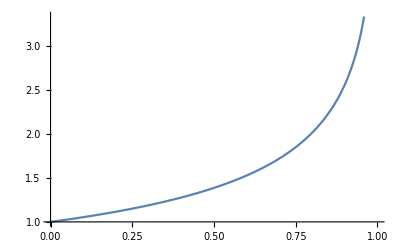

```mathematica
Plot[(-Log[1-x])/x,{x,0,1}]
```

```mathematica
FullSimplify[Integrate[f[e]/e,{e,eesc*p,∞}]]
```

ConditionalExpression[(1.59577 ⅇ^(-(eesc p)/ebar) nχ)/ebar^0.5,Re[ebar]>0]

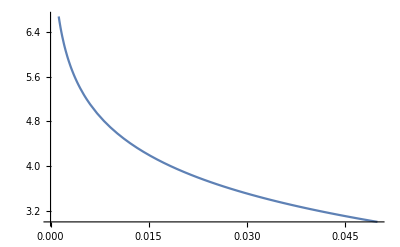

```mathematica
Plot[-Log[x],{x,0,0.05}]
```

```mathematica
(*SELF CAPTURE*)
```

```mathematica
DSolve[{nx'[t]==cc-ca*nx[t]^2,nx[0]==0},nx[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{nx[t]→(√cc Tanh[√ca √cc t])/(√ca)}}

```mathematica
n=10;
```

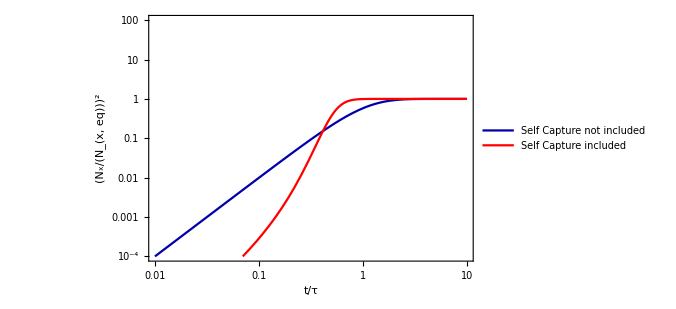

```mathematica
LogLogPlot[{Tanh[x]^2,(1/(n/2+√(n^2/4+1)))^2*(Tanh[√(n^2/4+1)*x]/(√(n^2/4+1)-n/2*Tanh[√(n^2/4+1)*x]))^2},{x,10^-2,10},PlotRange->{10^-4,10^2},PlotStyle->{Darker[Blue],Red},Frame->True,FrameLabel->{"t/τ","(N_x/(N_(x, eq)))^2"},FrameStyle->Directive[14, "Times",Black],ImageSize->500,PlotLegends->{"Self Capture not included","Self Capture included"}]
```

```mathematica
Assuming[cs≥0,DSolve[{nx'[t]==cc+cs*nx[t]-ca*nx[t]^2,nx[0]==0},nx[t],t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{nx[t]→(cs+√(-4 ca cc-cs^2) Tan[1/2 (-√(-4 ca cc-cs^2) t-2 ArcCos[-(√(4 ca cc+cs^2))/(2 √ca √cc)])])/(2 ca)},{nx[t]→(cs+√(-4 ca cc-cs^2) Tan[1/2 (-√(-4 ca cc-cs^2) t+2 ArcCos[-(√(4 ca cc+cs^2))/(2 √ca √cc)])])/(2 ca)}}

```mathematica
Integrate[1/(cc+cs*nx-ca*nx^2),nx]
```

-(2 ArcTan[(-cs+2 ca nx)/(√(-4 ca cc-cs^2))])/(√(-4 ca cc-cs^2))

```mathematica
ArcTan[ⅈ*x]
```

ⅈ ArcTanh[x]

```mathematica
Assuming[cs>0,Solve[ArcTanh[(cs*ζ)/2]-ArcTanh[(cs*ζ)/2-ζ*ca*nx]==t/ζ,nx]]
```

{{nx→ConditionalExpression[(cs ζ-2 Tanh[(-t+ζ ArcTanh[(cs ζ)/2])/ζ])/(2 ca ζ),(Re[(-t+ζ ArcTanh[(cs ζ)/2])/ζ]<0&&-π/2<Im[(-t+ζ ArcTanh[(cs ζ)/2])/ζ]≤π/2)||(Re[(-t+ζ ArcTanh[(cs ζ)/2])/ζ]==0&&-π/2<Im[(-t+ζ ArcTanh[(cs ζ)/2])/ζ]<π/2)||(Re[(-t+ζ ArcTanh[(cs ζ)/2])/ζ]>0&&-π/2≤Im[(-t+ζ ArcTanh[(cs ζ)/2])/ζ]<π/2)]}}

```mathematica
Integrate[u*Exp[(-3*u^2)/(2*vbar^2)],{u,0,∞}]
```

ConditionalExpression[vbar^2/3,Re[vbar^2]>0]

```mathematica
Integrate[u^3*Exp[(-3*u^2)/(2*vbar^2)],{u,0,∞}]
```

ConditionalExpression[(2 vbar^4)/9,Re[vbar^2]>0]

```mathematica
Integrate[1/(1-(z*β)),{z,0,1}]
```

ConditionalExpression[-Log[1-β]/β,Re[β]≤1||β∉Reals]

```mathematica
(*CALCULATION OF ϵ*)
```

```mathematica
u=600*10^3;(*in m/s*)
```

```mathematica
kb=1.38*10^-23;(*in J/K*)
conv=1.78*10^-27;(*conversion factor from Gev to Kg*)
```

```mathematica
ϵ[T_,mx_,ve_]=(3*kb*T)/(mx*conv*(u^2+ve^2));(*mx in Gev*)
```

```mathematica
ϵ[10^10,10^5,10^5*10^3](*For Neutron Star*)
```

2.32576×10^-7

```mathematica
ϵ[10^5,10^5,10^5*10^3](*For White Dwarf*)
```

2.32576×10^-12

```mathematica
ϵ[6000,10^5,11.2*10^3](*For Earth*)
```

3.87505×10^-9

```mathematica
ϵ[1.57*10^7,10^5,618*10^3] (*For Sun*)
```

4.92176×10^-6

```mathematica
(*DISTRIBUTION OF Z*)
```

```mathematica
δ=0.01;
```

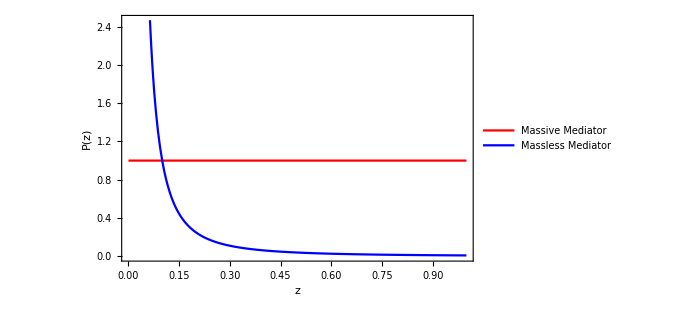

```mathematica
Plot[{1,δ/z^2},{z,0,1},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["z",FontSize->15],Style["P(z)",FontSize->15]},ImageSize->500,PlotStyle->{Red,Blue},PlotLegends->{"Massive Mediator","Massless Mediator"}]
```